# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Wisniacki chain\Mixed environment states

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Heisenberg with noise

```mathematica
Clear[Noisyheinsenberg];
Noisyheinsenberg[hz_,L_] := Module[{NNindices,a,b},
	NNindices=Normal[SparseArray[Thread[{#,#+1}->1],{L}]&/@Range[L-1]];
	a=N[Normal[Total[Join[(Pauli/@NNindices),(Pauli/@(2NNindices)),(Pauli/@(3NNindices))]]]];
	b=DiagonalMatrix[hz].Normal[Total[(Pauli[3#]&/@IdentityMatrix[L])]];
	a+b
]
```

# Mixed states

```mathematica
Clear[newsuper];
newsuper[t_,ψ0E_,eigVals_,eigVecs_,L_]:=Module[{ψf,ρfSE,basis=Table[VectorFromKetInComputationalBasis[i],{i,Tuples[{0,1},(L-1)]}]},ψf=Total[Table[Sqrt[ψ0E[[i]]]*StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],basis[[i]]],eigVals,eigVecs]&/@{{0},{1}},{i,Length[basis]}]];
ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];Transpose[ Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&/@ρfSE ]
]
```

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=ConstantArray[1/2^(L-1),2^(L-1)]
```

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

```mathematica
t=1;
superop=newsuper[t,ψe,eigenval,eigenvec,L];
```

```mathematica
Eigenvalues[superop]//Chop
```

{1.,-0.263616+0.313819 ⅈ,-0.263616-0.313819 ⅈ,0.258964}

```mathematica
Eigenvalues[Reshuffle[(1/2)superop]]
Eigenvalues[Reshuffle[(1/2)superop]]//Total
```

{0.586859,0.368088,0.0261938,0.0188591}

1.

```mathematica
tlist=Range[0,20,0.1];
```

```mathematica
data=Table[Transpose[{ConstantArray[t,4],Eigenvalues[Reshuffle[(1/2)newsuper[t,ψe,eigenval,eigenvec,L]]]}],{t,tlist}];
```

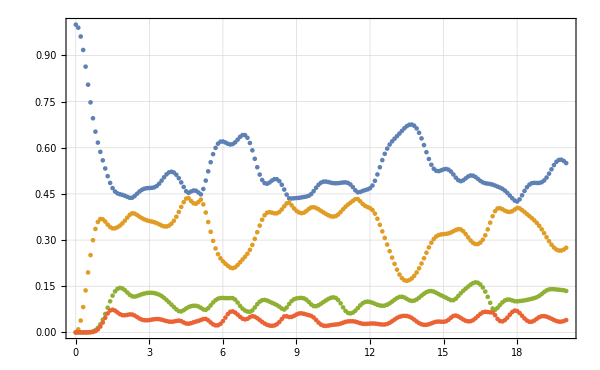

```mathematica
ListPlot[Transpose[data],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```